```mathematica
Grid[MapThread[Prepend,{Prepend[Table[(2s k)^(s k),{s,2,5},{k,2,5}],{"s"->2,"s"->3,"s"->4,"s"->5}],{"","k"->2,"k"->3,"k"->4,"k"->5}}],Frame->All,Background->{None,{None,Yellow}}]
```

| s→2 | s→3 | s→4 | s→5
k→2 | 4096 | 2985984 | 4294967296 | 10240000000000
k→3 | 2985984 | 198359290368 | 36520347436056576 | 14348907000000000000000
k→4 | 4294967296 | 36520347436056576 | 1208925819614629174706176 | 109951162777600000000000000000000
k→5 | 10240000000000 | 14348907000000000000000 | 109951162777600000000000000000000 | 2980232238769531250000000000000000000000000

```mathematica
ChangeNumbering[number_,{S_,K_}]:=FromDigits[Flatten[Reverse[Partition[PadLeft[IntegerDigits[number,2S K],S K],2]]],2S K]
```

```mathematica
MyInstructionsTable[nb_]:=({(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,2])/4,Mod[(#-Mod[#,2])/2,2],Mod[#,2]}&/@PadLeft[IntegerDigits[nb,12],6])
```

```mathematica
activetriplets[nb_]:=({(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,2])/4,Mod[(#-Mod[#,2])/2,2],Mod[#,2]}&/@PadLeft[IntegerDigits[nb,12],6])
```

```mathematica
activetriplets[1]
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,1}}

## Toutes les MT3 (inventaire presque complet) :

```mathematica
(*First Run*)       t=AbsoluteTime[];loop=halt=0;remise={};
shortloopings=Flatten[Reap[Do[         Clear[a]; i=0;a[_]=0;n=ninf=-1;sigma=0;res={{0,-1,{0}}};

While[n<0 && i<2,{activatedtriplet=activetriplets[nb][[6-2sigma-a[n]]];a[n]=activatedtriplet[[2]];n=n-1+2activatedtriplet[[3]];ninf=Min[n,ninf];sigma=activatedtriplet[[1]];res=AppendTo[res,{sigma,n,Table[a[j],{j,ninf,n}]}]   };i++];

If[n==0,halt=halt+1,    {corners=#[[1]]&/@Position[res,-1,2];left=Min[#[[2]]&/@res];Do[{corners=AppendTo[corners,Select[#[[1]]&/@Position[res,k,2],#>Max[corners]&]]},{k,-2,left,-1}];listetest={#[[1]],FromDigits[#[[3]],2]}&/@res[[Flatten[corners]]];If[Length[Union[listetest]]≠Length[listetest],Sow[nb],]}    ]
    
           ,{nb,0,2985984-1,2}]][[2]]];AbsoluteTime[]-t
```

242.384973

```mathematica
Length[shortloopings]
```

870912

```mathematica
corners
```

{1,{2},{3},{4},{5}}

```mathematica
res
```

{{0,-1,{0}},{2,-2,{0}},{2,-1,{1,1}},{2,0,{1,1,0}}}

```mathematica
Position[res,-2,2]
```

{{2,2}}

```mathematica
{halt,loop,Length[remise]}
```

{248832,1002240,241920}

```mathematica
{halt,loop,Length[Flatten[remise[[2]]]]}
```

{248832,1072224,171936}

```mathematica
Total[{248832,1072224,171936}]
```

1492992

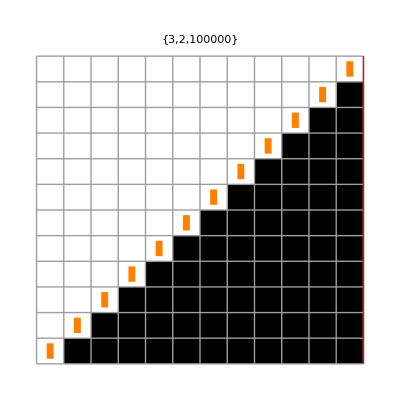
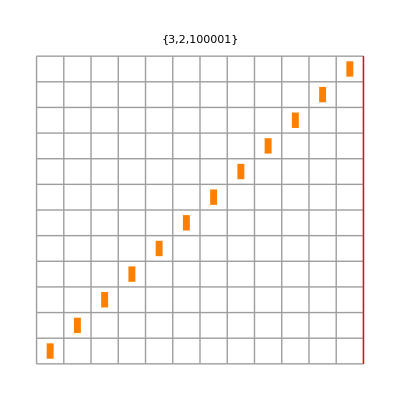
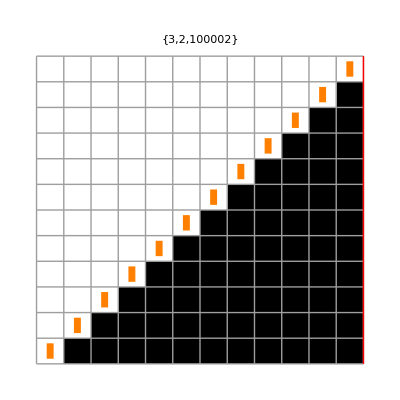
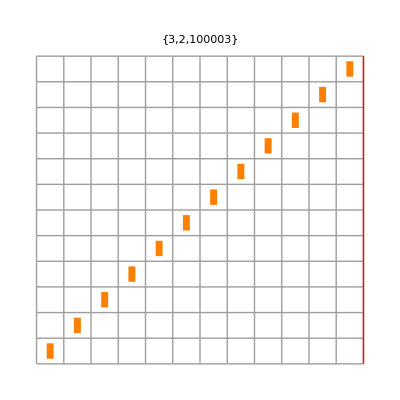
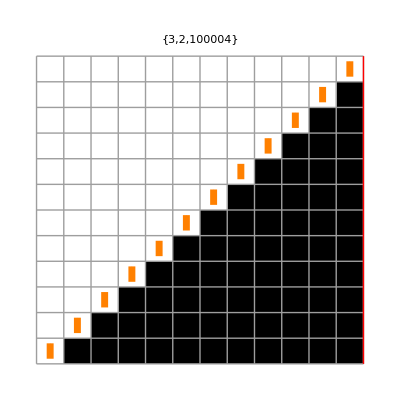
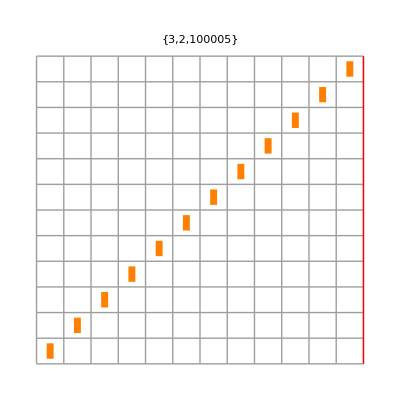
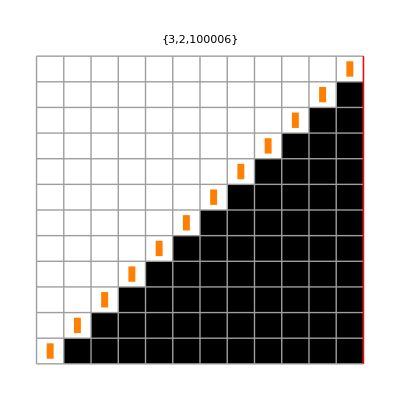
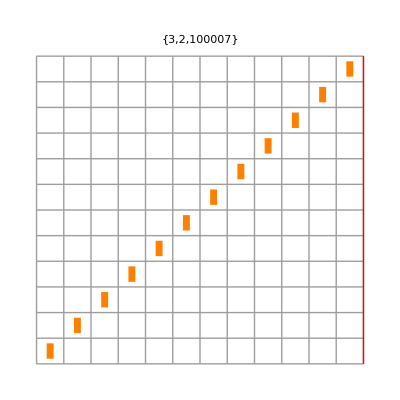
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
s=3;k=2;limit=12;Do[{Clear[tm];tm=TuringMachine[{ChangeNumbering[shortloopings[[nb]],{3,2}],s,k},{{1,0},{{},0}},limit];
step=If[MemberQ[Transpose[Transpose[tm][[1]]][[3]],1],First[Position[Transpose[Transpose[tm][[1]]][[3]],1]][[1]],limit]-1;Clear[tm];tm=TuringMachine[{ChangeNumbering[shortloopings[[nb]],{3,2}],s,k},{{1,0},{{},0}},step];
delta=If[1-Min[Transpose[Transpose[tm][[1]]][[3]]]>0,1-Min[Transpose[Transpose[tm][[1]]][[3]]],0];
tm12=Transpose[Transpose[tm][[1]]][[2]];tm11=Transpose[Transpose[tm][[1]]][[1]];f[shortloopings[[nb]]]=ArrayPlot[Last/@tm,Mesh->True,PlotLabel->{s,k,nb},LabelStyle->Directive[Bold],Epilog->{{Red,Thick,Line[{{delta,0},{delta,step+1}}]},Orange,Thickness[0.15/(step+1)],Arrowheads[0.5/(step+1)],Table[Rotate[Arrow[{{-1/2+tm12[[i]],2/10+1+step-i},{-1/2+tm12[[i]],4/5+1+step-i}}],-2π/s(tm11[[i]]-1)],{i,step+1}]}]},{nb,0,127}];Table[f[shortloopings[[nb]]],{nb,0,127}]
```

```mathematica
Table[shortloopings[[nb]],{nb,128}]
```

{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100,102,104,106,108,110,112,114,116,118,120,122,124,126,128,130,132,134,136,138,140,142,144,146,148,152,154,156,158,160,164,166,168,170,172,176,178,180,182,184,188,190,192,194,196,200,202,204,206,208,212,214,216,218,220,224,226,228,230,232,236,238,240,242,244,248,250,252,254,256,260,262,264,266,268,272,274,276}

```mathematica
FindSequenceFunction[Table[shortloopings[[nb]],{nb,1024}]]
```

FindSequenceFunction[{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100,102,104,106,108,110,112,114,116,118,120,122,124,126,128,130,132,134,136,138,140,142,144,146,148,152,154,156,158,160,164,166,168,170,172,176,178,180,182,184,188,190,192,194,196,200,202,204,206,208,212,214,216,218,220,224,226,228,230,232,236,238,240,242,244,248,250,252,254,256,260,262,264,266,268,272,274,276,278,280,284,286,288,290,292,294,296,298,300,302,304,306,308,310,312,314,316,318,320,322,324,326,328,330,332,334,336,338,340,342,344,346,348,350,352,354,356,358,360,362,364,366,368,370,372,374,376,378,380,382,384,386,388,390,392,394,396,398,400,402,404,406,408,410,412,414,416,418,420,422,424,426,428,430,432,434,440,442,444,446,452,454,456,458,464,466,468,470,476,478,480,482,488,490,492,494,500,502,504,506,512,514,516,518,524,526,528,530,536,538,540,542,548,550,552,554,560,562,564,566,572,574,576,578,580,582,584,586,588,590,592,594,596,598,600,602,604,606,608,610,612,614,616,618,620,622,624,626,628,630,632,634,636,638,640,642,644,646,648,650,652,654,656,658,660,662,664,666,668,670,672,674,676,678,680,682,684,686,688,690,692,694,696,698,700,702,704,706,708,710,712,714,716,718,720,722,728,730,732,734,740,742,744,746,752,754,756,758,764,766,768,770,776,778,780,782,788,790,792,794,800,802,804,806,812,814,816,818,824,826,828,830,836,838,840,842,848,850,852,854,860,862,864,866,868,870,872,874,876,878,880,882,884,886,888,890,892,894,896,898,900,902,904,906,908,910,912,914,916,918,920,922,924,926,928,930,932,934,936,938,940,942,944,946,948,950,952,954,956,958,960,962,964,966,968,970,972,974,976,978,980,982,984,986,988,990,992,994,996,998,1000,1002,1004,1006,1008,1010,1016,1018,1020,1022,1028,1030,1032,1034,1040,1042,1044,1046,1052,1054,1056,1058,1064,1066,1068,1070,1076,1078,1080,1082,1088,1090,1092,1094,1100,1102,1104,1106,1112,1114,1116,1118,1124,1126,1128,1130,1136,1138,1140,1142,1148,1150,1152,1154,1160,1162,1164,1166,1172,1174,1176,1178,1184,1186,1188,1190,1196,1198,1200,1202,1208,1210,1212,1214,1220,1222,1224,1226,1232,1234,1236,1238,1244,1246,1248,1250,1256,1258,1260,1262,1268,1270,1272,1274,1280,1282,1284,1286,1292,1294,1296,1298,1304,1306,1308,1310,1316,1318,1320,1322,1328,1330,1332,1334,1340,1342,1344,1346,1352,1354,1356,1358,1364,1366,1368,1370,1376,1378,1380,1382,1388,1390,1392,1394,1400,1402,1404,1406,1412,1414,1416,1418,1424,1426,1428,1430,1436,1438,1440,1442,1448,1450,1452,1454,1460,1462,1464,1466,1472,1474,1476,1478,1484,1486,1488,1490,1496,1498,1500,1502,1508,1510,1512,1514,1520,1522,1524,1526,1532,1534,1536,1538,1544,1546,1548,1550,1556,1558,1560,1562,1568,1570,1572,1574,1580,1582,1584,1586,1592,1594,1596,1598,1604,1606,1608,1610,1616,1618,1620,1622,1628,1630,1632,1634,1640,1642,1644,1646,1652,1654,1656,1658,1664,1666,1668,1670,1676,1678,1680,1682,1688,1690,1692,1694,1700,1702,1704,1706,1712,1714,1716,1718,1724,1726,1728,1730,1732,1734,1736,1738,1740,1742,1744,1746,1748,1750,1752,1754,1756,1758,1760,1762,1764,1766,1768,1770,1772,1774,1776,1778,1780,1782,1784,1786,1788,1790,1792,1794,1796,1798,1800,1802,1804,1806,1808,1810,1812,1814,1816,1818,1820,1822,1824,1826,1828,1830,1832,1834,1836,1838,1840,1842,1844,1846,1848,1850,1852,1854,1856,1858,1860,1862,1864,1866,1868,1870,1872,1874,1876,1880,1882,1884,1886,1888,1892,1894,1896,1898,1900,1904,1906,1908,1910,1912,1916,1918,1920,1922,1924,1928,1930,1932,1934,1936,1940,1942,1944,1946,1948,1952,1954,1956,1958,1960,1964,1966,1968,1970,1972,1976,1978,1980,1982,1984,1988,1990,1992,1994,1996,2000,2002,2004,2006,2008,2012,2014,2016,2018,2020,2022,2024,2026,2028,2030,2032,2034,2036,2038,2040,2042,2044,2046,2048,2050,2052,2054,2056,2058,2060,2062,2064,2066,2068,2070,2072,2074,2076,2078,2080,2082,2084,2086,2088,2090,2092,2094,2096,2098,2100,2102,2104,2106,2108,2110,2112,2114,2116,2118,2120,2122,2124,2126,2128,2130,2132,2134,2136,2138,2140,2142,2144,2146,2148,2150,2152,2154,2156,2158,2160,2162,2168,2170,2172,2174,2180,2182,2184,2186,2192,2194,2196,2198,2204,2206,2208,2210,2216,2218,2220,2222,2228,2230,2232,2234,2240,2242,2244,2246,2252,2254,2256,2258,2264,2266,2268,2270,2276,2278,2280,2282,2288,2290,2292,2294,2300,2302,2304,2306,2308,2310,2312,2314,2316,2318,2320,2322,2324,2326,2328,2330,2332,2334,2336,2338,2340,2342,2344,2346,2348,2350,2352,2354,2356,2358,2360,2362,2364,2366,2368,2370,2372,2374,2376,2378,2380,2382,2384,2386,2388,2390,2392,2394,2396,2398,2400,2402,2404,2406,2408,2410,2412,2414,2416,2418,2420,2422,2424,2426,2428,2430,2432,2434,2436,2438,2440,2442,2444,2446,2448,2450,2456,2458,2460,2462,2468,2470,2472,2474,2480,2482,2484,2486,2492,2494}]

```mathematica
s=3;k=2;limit=12;Do[{Clear[tm];tm=TuringMachine[{ChangeNumbering[nb,{3,2}],s,k},{{1,0},{{},0}},limit];
step=If[MemberQ[Transpose[Transpose[tm][[1]]][[3]],1],First[Position[Transpose[Transpose[tm][[1]]][[3]],1]][[1]],limit]-1;Clear[tm];tm=TuringMachine[{ChangeNumbering[nb,{3,2}],s,k},{{1,0},{{},0}},step];
delta=If[1-Min[Transpose[Transpose[tm][[1]]][[3]]]>0,1-Min[Transpose[Transpose[tm][[1]]][[3]]],0];
tm12=Transpose[Transpose[tm][[1]]][[2]];tm11=Transpose[Transpose[tm][[1]]][[1]];f[nb]=ArrayPlot[Last/@tm,Mesh->True,PlotLabel->{s,k,nb},LabelStyle->Directive[Bold],Epilog->{{Red,Thick,Line[{{delta,0},{delta,step+1}}]},Orange,Thickness[0.15/(step+1)],Arrowheads[0.5/(step+1)],Table[Rotate[Arrow[{{-1/2+tm12[[i]],2/10+1+step-i},{-1/2+tm12[[i]],4/5+1+step-i}}],-2π/s(tm11[[i]]-1)],{i,step+1}]}]},{nb,190,210}];Table[f[nb],{nb,190,210}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[-2 (4+(-1)^j-3 j),{j,10}]
```

{0,2,12,14,24,26,36,38,48,50}

```mathematica
Table[-2 (4+(-1)^j-3 j),{j,10}]
```

{0,2,12,14,24,26,36,38,48,50}

```mathematica
s=3;k=2;limit=125;Do[{Clear[tm];tm=TuringMachine[{ChangeNumbering[remise[[nb]],{3,2}],s,k},{{1,0},{{},0}},limit];
step=If[MemberQ[Transpose[Transpose[tm][[1]]][[3]],1],First[Position[Transpose[Transpose[tm][[1]]][[3]],1]][[1]],limit]-1;Clear[tm];tm=TuringMachine[{ChangeNumbering[remise[[nb]],{3,2}],s,k},{{1,0},{{},0}},step];
delta=If[1-Min[Transpose[Transpose[tm][[1]]][[3]]]>0,1-Min[Transpose[Transpose[tm][[1]]][[3]]],0];
tm12=Transpose[Transpose[tm][[1]]][[2]];tm11=Transpose[Transpose[tm][[1]]][[1]];f[remise[[nb]]]=ArrayPlot[Last/@tm,Mesh->True,PlotLabel->{s,k,nb},LabelStyle->Directive[Bold],Epilog->{{Red,Thick,Line[{{delta,0},{delta,step+1}}]},Orange,Thickness[0.15/(step+1)],Arrowheads[0.5/(step+1)],Table[Rotate[Arrow[{{-1/2+tm12[[i]],2/10+1+step-i},{-1/2+tm12[[i]],4/5+1+step-i}}],-2π/s(tm11[[i]]-1)],{i,step+1}]}]},{nb,1243,1243}];Table[f[remise[[nb]]],{nb,1243,1243}]
```

{-Graphics-}